```mathematica
Bode Plot program for an arbitrary frequency response
```

```mathematica
H (ⅉ ω)=(K ⅉω (ⅉω/Subscript[z, 1]+1)...(ⅉω/Subscript[z, n]+1))/(ⅉω (ⅉω/Subscript[p, 1]+1)... (ⅉω/Subscript[p, n]+1))
|H(ⅉω)|=20 Subscript[log, 10](K)+(∑_(i=1)^n 20 Subscript[log, 10]|1+ⅉω/Subscript[z, i]|)-(∑_(j=1)^m 20 Subscript[log, 10]|1+ⅉω/Subscript[p, j]|)
ϕ(ⅉω)=∑_(i=1)^n arctan(ω/Subscript[z, i])-∑_(j=1)^m arctan(ω/Subscript[p, j])
```

1

{2,55,ⅈ ω}

0

H(ⅉω)= (40 (1+(ⅈ ω)/55) (1+(ⅈ ω)/2))/((1+(ⅈ ω)/80) (1+(ⅈ ω)/60) (1+(ⅈ ω)/40) (1+(ⅈ ω)/20))

{2,55}

{20,40,60,80}

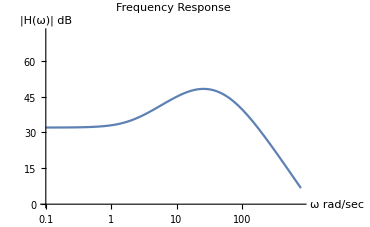

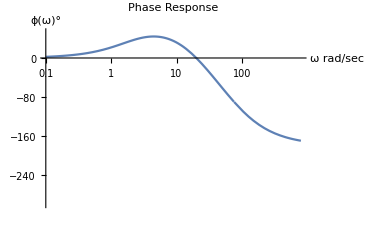

```mathematica
(*Start of Program*)
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];
n = Input["Enter The Number Of Poles"];
m=Input["Enter The Number Of Zeroes"];
listOfPoles =Table[Input["Enter The Value Of The nth nonzero Pole"],n];
listOfZeroes=Table[Input["Enter The Value Of The nth nonzero Zero"],m];
zeroFlag=Input["Is There A Zero At The Origin? Enter 1 For Yes Or 0 For No"]
If[zeroFlag==1,Append[listOfZeroes,ⅉ ω]]
poleFlag=Input["Is There A Pole At The Origin? Enter 1 For Yes Or 0 For No"]
If[poleFlag==1&&zeroFlag==0,Append[listOfPoles,ⅉ ω]]
H[ω_]:=K*Times@@(1/(1+(ⅉ*ω)/#))&[listOfPoles]*Times@@(1+(ⅉ*ω)/#)&[listOfZeroes](*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
StringForm["H(ⅉω)= ``",H[ω]]
Print[listOfZeroes]
Print[listOfPoles]
listOfMagnitudes=20*Log[10,Abs[H[#]]]&/@Join[listOfPoles,listOfZeroes]//N;
peakdB=Max[listOfMagnitudes];
mindB=Which[peakdB-Min[listOfMagnitudes]≤50,0,peakdB-Min[listOfMagnitudes]>50,Min[listOfMagnitudes]];
listOfPhases=180/π*Arg[H[#]]&/@Join[listOfPoles,listOfZeroes]//N;
peakPhase=Which[Max[listOfPhases]<0,0,Max[listOfPhases]>0,Max[listOfPhases]];
(*ϕ[ω_]:=Arg[K]+(Plus@@-(180/π*ArcTan[ω/#]&[listOfPoles]))+(Plus@@(180/π*ArcTan[ω/#]&[listOfZeroes]))*)
ϕ[ω_]:=180/π Arg[H[ω]]
LogLinearPlot[20*Log[10,Abs[H[ω]]],{ω,0.1,10*Max[listOfPoles]},PlotRange->{{0.1,10*Max[listOfPoles]},{1.5*mindB,1.5*peakdB}},PlotLabel->"Frequency Response", AxesLabel->{"ω rad/sec","|H(ω)| dB"}]
LogLinearPlot[ϕ[ω], {ω,0.1,10*Max[listOfPoles]},PlotRange->{{0.1,10*Max[listOfPoles]},{-300,1.5 peakPhase}},PlotLabel->"Phase Response", AxesLabel->{"ω rad/sec","ϕ(ω)°"}]
```